```mathematica
SetDirectory["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Практика\\Программа\\project"];
```

```mathematica
determinePointPosition[lineStartPoint_,lineEndPoint_,pointToCheck_]:=
Block[{result,positionLine},
result:=(pointToCheck[[1]]-lineStartPoint[[1]])*(lineEndPoint[[2]]-lineStartPoint[[2]])-(pointToCheck[[2]]-lineStartPoint[[2]])*(lineEndPoint[[1]]-lineStartPoint[[1]]);
positionLine:=Which[result<0,"down",result>0,"up",result==0,"within" ]; positionLine];
(*Визуализация*)
vizualization[File_String]:=Block[{Points =Rest@Import[File, "Table"], ConvexHull = SimpleSearchConvexHullFile[File]},Graphics[{Point@Points, Red,Line@Append[ConvexHull,ConvexHull[[1]]]}]];
(*Метод перебора*)
SimpleSearchConvexHull[Points_List] := Block[{points=Points ,n ,convexHullPoints = {},pointXmin,formerPoint,latterPoint,candidatePoint,indexXmin,i,j,indexPoint,q1,q2,endAlgorithm,comparator},
n =Length[points];
(*Нахождение нижней точки из самых левых*)
indexXmin=1;
For[i= 2, i≤ n, ++i,
If[points⟦i,1⟧<points⟦indexXmin,1⟧ || 
(points⟦i,1⟧==points⟦indexXmin,1⟧ &&  
points⟦i,2⟧<points⟦indexXmin,2⟧),
indexXmin=i]];
AppendTo[convexHullPoints,points[[indexXmin]]];
AppendTo[points,points[[indexXmin]]];
points=Delete[points,indexXmin];
formerPoint=convexHullPoints[[1]];(*основная точка*)
endAlgorithm=True;
While[endAlgorithm,For[i=2;j=1,i≤ n-Length[convexHullPoints] +1,++i, 
latterPoint=points[[j]];(*следующая точка*)
candidatePoint = points[[i]];(*точка кандидат*)
comparator=determinePointPosition[formerPoint,latterPoint,candidatePoint];
If[comparator =="down",j=i];
q1=latterPoint-formerPoint;
q2=candidatePoint-formerPoint;
If[comparator =="within",If[Norm[q1]<Norm[q2],j=i]];];
If[convexHullPoints[[1]]!=points[[j]],AppendTo[convexHullPoints,points[[j]]];formerPoint=points[[j]]; points=Delete[points,j]; j=1,endAlgorithm=False];];convexHullPoints];

SimpleSearchConvexHullFile[from_String]:=Block[{list=Rest@Import[from, "Table"], result,time},result=SimpleSearchConvexHull[list];Print[Length@result ];result];

Timing@SimpleSearchConvexHullFile["test.txt"]
```

9

{0.015625,{{-0.949363,-0.94019},{-0.886127,-0.174782},{-0.655057,0.565772},{-0.321485,0.945953},{0.168952,0.970351},{0.483897,0.916722},{0.641655,0.542579},{0.67236,0.394648},{0.0455653,-0.778337}}}

9

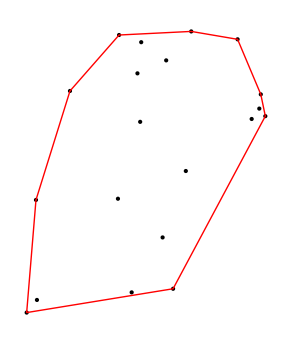

```mathematica
vizualization["test.txt"]
```